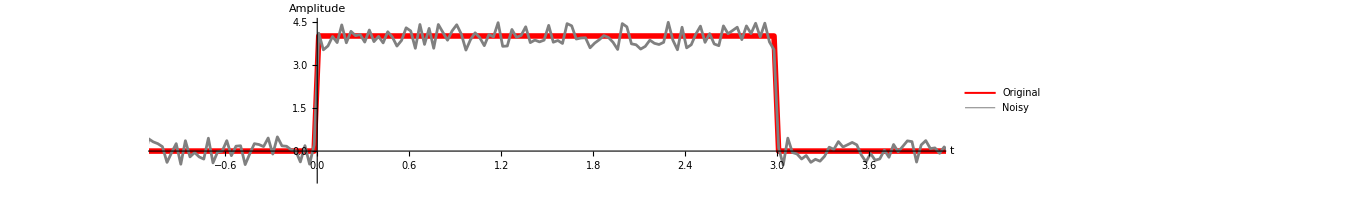

```mathematica
(*Окно, чтобы показать исходный и шумный сигнал*)
a=4;
t1=0;
t2=3;
c=0;
d=2;
b=0.5;

T=10;
dt=0.03;
tValues=Range[-T/2,T/2,dt];
n=Length[tValues];

vValues=Table[-1/(2 dt)+(k-1)*1/T,{k,n}];

gVals=Table[If[t1<=t<=t2,a,0],{t,tValues}];
xi=RandomReal[{-1,1},n];
uVals=gVals+b*xi+c*Sin[d*tValues];

ListLinePlot[{Transpose[{tValues,gVals}],Transpose[{tValues,uVals}]}, 
AspectRatio->0.2,
PlotLegends->Placed[{"Original", "Noisy"},Right],
 PlotStyle->{{Red,Thickness[0.004]},{Gray, Thickness[0.002]}},
AxesLabel->{"t","Amplitude"},
ImageSize->1000,
PlotRange->{{-1, 4},{-1,4.5}}
]
```